```mathematica
SymbolHighlight[s_,e_]:=Block[{conv,elim={e[[1]],e[[2]]}},
conv=SymbolToSets[s];
conv=Map[Select[#,!MemberQ[elim,#]&]&,conv];
conv=Select[conv,#≠{}&];
conv=Sort[Map[Sort,conv],Min[#1]<Min[#2]&];
SetsToSymbol[conv]
]
```

```mathematica
SymbolHighlight[v15x24x3x67,1<->2]
```

v3x4x5x67

```mathematica
SymbolHighlight [   v1x24x37x5x6,1<->2]
```

{{4},{3,7},{5},{6}}

{{4},{3,7},{5},{6}}

{{4},{5},{6},{3,7}}

{{3,7},{4},{5},{6}}

v37x4x5x6

```mathematica
MixSymbols[{a,b,d},{a,b,c}]
```

{a,b,d,c}

```mathematica
MixSymbols[set1_,set2_]:=Block[{result=Sort[DeleteDuplicates[Join[set1,set2]],CompareSymbols]},
Map[
Block[{color,exp},
If[MemberQ[set1,#],
If[MemberQ[set2,#],
color=Darker[Green];
exp="Symbol is in full and delete";
,
color=Darker[Red];
exp="Symbol is in full bot NOT delete";
]
,
color=Orange;
exp="Symbol is in delte but NOT full";
];
Tooltip[Style[#,color],exp]
]&
,
result]
]
```

```mathematica
FindMinEdges6[g_]:=Block[{minChrom=Null,min=Null,global=ChromaticPolynomial[g,4],removed,chrom,form},
Table[
removed=EdgeDelete[g,e];
chrom=ChromaticPolynomial[removed,4];
If[minChrom==Null, 
minChrom=chrom;
min={},
If[chrom<minChrom,
minChrom=chrom;
min={}
]];
If[chrom==minChrom,AppendTo[min,e]];
,{e, EdgeList[g]}
];
form=FindFullFormula[g];
min=Table[
With[{del=FindFullFormula[EdgeDelete[g,e]]},
e<->Graph[g,GraphHighlight->e,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]<->Graph[FormulaGraphReverse2[SetDifference[ListofVars[del],ListofVars[form]]],ImageSize->600]<-> 
With[{left=Map[SymbolHighlight[#,e]&,Select[form,SymbolLevel[#]≤5&]],
right=Map[SymbolHighlight[#,e]&,Select[del,SymbolLevel[#]<=5&]]},
Multicolumn[MixSymbols[left,right],4]
]
],{e,Take[min,1]}];
{global,minChrom,min}
]
```

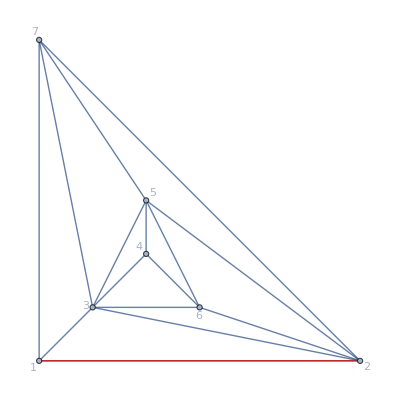
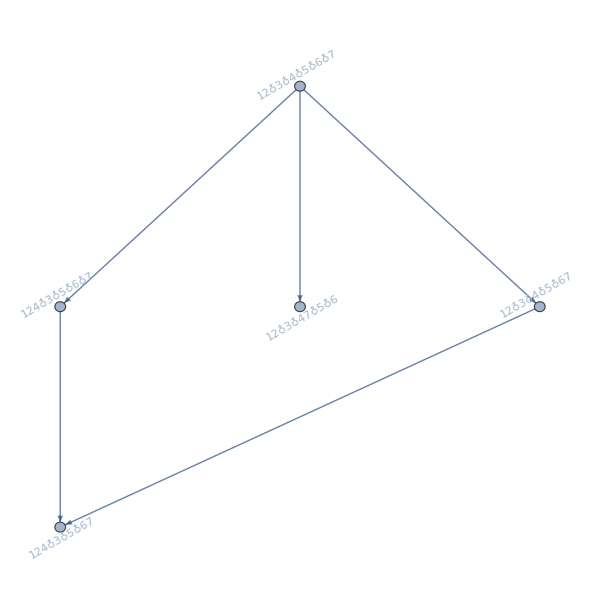
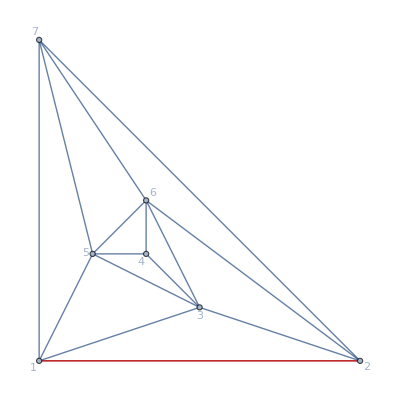
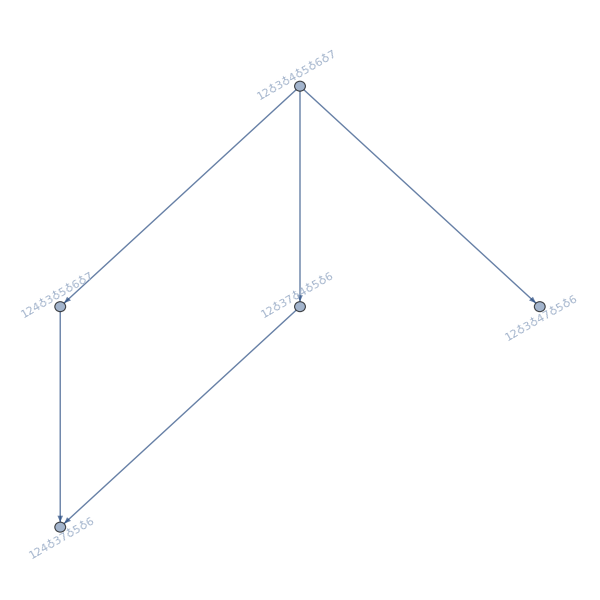
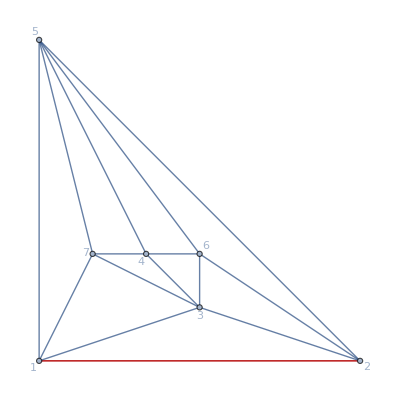
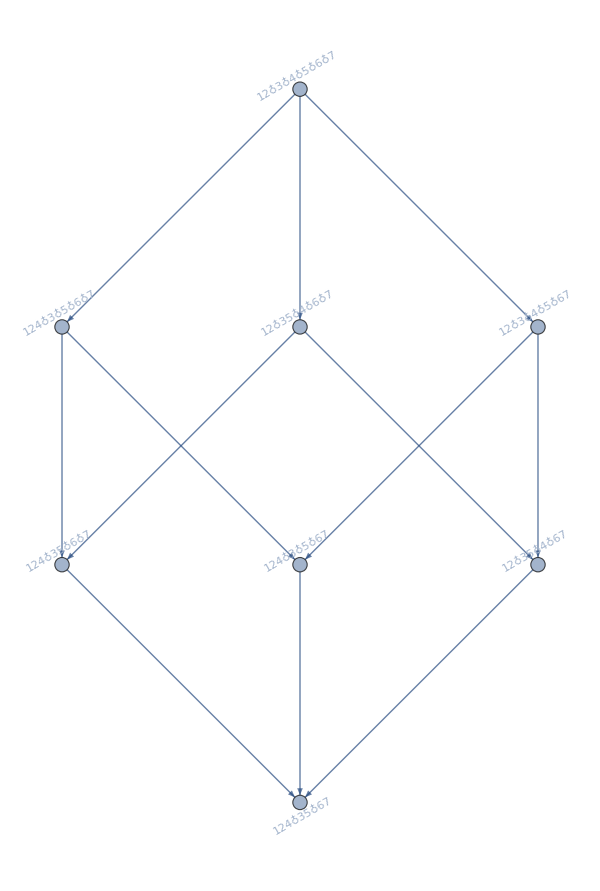
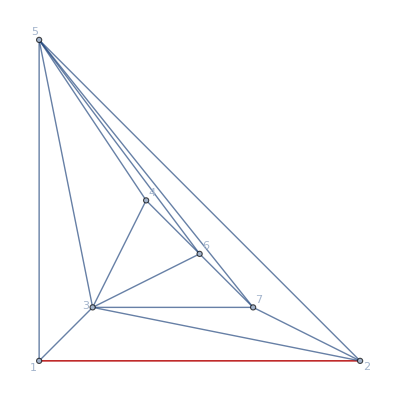
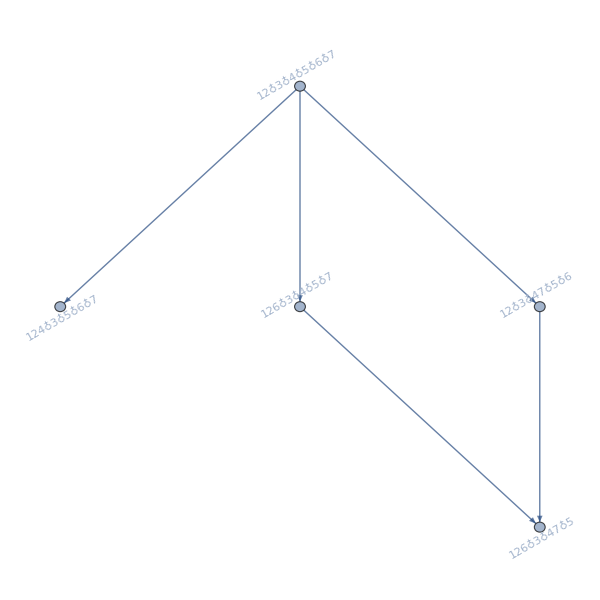
5 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x7 | v3x4x5x67 | v3x5x6x47 | }
6 | 96 | 120 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x7 | v3x5x6x47 | v4x5x6x37 | }
7 | 120 | 216 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x7 | v3x4x5x67 | v4x6x7x35 | v4x35x67}
8 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x7 | v3x5x6x47 |  | }
9 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x7 | v3x4x6x57 | v3x5x6x47 | }
10 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x78 | v3x5x6x8x47 | v5x6x34x78 | 
v3x4x5x8x67 | v5x6x7x8x34 | v5x8x34x67 | }
11 | 120 | 240 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x7x68 | v4x6x7x8x35 | v4x8x35x67 | 
v3x4x5x8x67 | v3x5x47x68 | v6x8x35x47 | 
v3x5x6x8x47 | v4x7x35x68 | v35x47x68 | }
12 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x78 | v3x5x6x8x47 | v3x6x45x78 | 
v3x4x5x8x67 | v3x6x7x8x45 | v3x8x45x67 | }
13 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x78 | v3x5x6x7x48 | v3x5x48x67 | 
v3x4x5x8x67 | v3x5x6x8x47 | v3x5x6x478 | }
14 | 96 | 192 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x78 | v4x5x7x8x36 | v4x5x36x78 | v36x47x58
v3x4x5x8x67 | v3x4x58x67 | v4x7x36x58 | 
v3x4x6x7x58 | v3x6x47x58 | v5x8x36x47 | }
15 | 96 | 192 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x8x67 | v3x5x6x8x47 | v3x5x48x67 | v5x6x38x47
v3x5x6x7x48 | v4x5x6x7x38 | v4x5x38x67 | }
16 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x78 | v3x4x6x7x58 | v3x5x48x67 | v3x6x47x58
v3x4x5x8x67 | v3x4x58x67 | v3x5x6x478 | }
17 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x78 | v4x5x6x7x38 | v3x5x6x478 | v5x6x38x47
v3x4x5x8x67 | v3x5x48x67 | v4x5x38x67 | }
18 | 72 | 168 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x7x68 | v4x5x6x8x37 | v4x5x37x68 | v6x8x35x47
v3x4x5x8x67 | v4x6x7x8x35 | v4x7x35x68 | v35x47x68
v3x5x6x8x47 | v3x5x47x68 | v4x8x35x67 | }
19 | 96 | 192 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x8x67 | v4x6x7x8x35 | v4x8x35x67 | v6x8x35x47
v3x5x6x8x47 | v5x6x7x8x34 | v5x8x34x67 | }
20 | 96 | 120 | {1<->2<->-Graphics-<->-Graphics-<->v3x4x5x6x78 | v3x5x6x8x47 | v3x5x6x478 | 
v3x4x5x7x68 | v4x5x6x8x37 | v4x5x37x68 | 
v3x5x6x7x48 | v3x5x47x68 | v5x6x37x48 | }

```mathematica
Monitor[TableForm[Table[With[{g=ReadGrof[k]},Prepend[FindMinEdges6[g],k]],{k,5,20}],TableDepth->3],{k,e}]
```

```mathematica
FindMinEdges7[g_]:=Block[{minChrom=Null,min=Null,global=ChromaticPolynomial[g,4],removed,chrom},
Table[
removed=EdgeDelete[g,e];
chrom=ChromaticPolynomial[removed,4];
If[minChrom==Null, 
minChrom=chrom;
min={},
If[chrom<minChrom,
minChrom=chrom;
min={}
]];
If[chrom==minChrom,AppendTo[min,e]];
,{e, EdgeList[g]}
];
min=Table[
With[{del=FindFullFormula1234[EdgeContract[g,e]],
del2=FindFullFormula1234[EdgeDelete[g,e]]},
e<->
With[{left=Map[SymbolHighlight[#,e]&,Select[del2,SymbolLevel[#]≤5&]],
right=Map[SymbolHighlight[#,e]&,Select[del,SymbolLevel[#]<=5&]]},
Multicolumn[MixSymbols[left,right],4]
]
],{e,Take[min,1]}];
{global,minChrom,min}
]
```

```mathematica
Map[SymbolHighlight[#,1<->2]&,FindFullFormula5[EdgeContract[ReadGrof[6],1<->2]]]
```

{v3x4x5x6x7,v3x47x5x6,v37x4x5x6}

```mathematica
Map[#->SymbolHighlight[#,1<->2]&,FindFullFormula5[EdgeDelete[ReadGrof[6],1<->2]]]
```

{v1x24x37x5x6→v37x4x5x6,v1x25x3x47x6→v3x47x5x6,v1x25x37x4x6→v37x4x5x6,v14x2x37x5x6→v37x4x5x6,v14x25x3x6x7→v3x4x5x6x7,v16x2x3x47x5→v3x47x5x6,v16x2x37x4x5→v37x4x5x6,v16x24x3x5x7→v3x4x5x6x7,v16x25x3x4x7→v3x4x5x6x7,v124x3x5x6x7→v3x4x5x6x7,v12x3x47x5x6→v3x47x5x6,v12x37x4x5x6→v37x4x5x6}

```mathematica
Monitor[TableForm[Table[With[{g=ReadGrof[k]},Prepend[FindMinEdges7[g],k]],{k,5,20}],TableDepth->3],{k,e}]
```

5 | 24 | 48 | {1<->2<->v3x4x5x67 |  |  | }
6 | 96 | 120 | {1<->2<->v37x4x5x6 | v3x47x5x6 |  | }
7 | 120 | 216 | {1<->2<->v35x4x6x7 | v3x4x5x67 | v35x4x67 | }
8 | 24 | 48 | {1<->2<->v3x47x5x6 |  |  | }
9 | 24 | 48 | {1<->2<->v3x4x57x6 |  |  | }
10 | 24 | 48 | {1<->2<->v34x5x67x8 |  |  | }
11 | 120 | 240 | {1<->2<->v35x47x6x8 | v35x4x67x8 | v35x4x68x7 | v35x47x68}
12 | 24 | 48 | {1<->2<->v3x45x67x8 |  |  | }
13 | 24 | 48 | {1<->2<->v3x478x5x6 |  |  | }
14 | 96 | 192 | {1<->2<->v36x4x58x7 | v36x4x5x78 | v3x4x58x67 | v36x47x58}
15 | 96 | 192 | {1<->2<->v38x47x5x6 | v38x4x5x67 | v3x48x5x67 | }
16 | 24 | 48 | {1<->2<->v3x4x58x67 |  |  | }
17 | 24 | 48 | {1<->2<->v38x4x5x67 |  |  | }
18 | 72 | 168 | {1<->2<->v35x47x6x8 | v35x4x68x7 | v35x47x68 | 
v35x4x67x8 | v37x4x5x68 |  | }
19 | 96 | 192 | {1<->2<->v34x5x67x8 | v35x47x6x8 | v35x4x67x8 | }
20 | 96 | 120 | {1<->2<->v37x48x5x6 | v37x4x5x68 | v3x478x5x6 | }

```mathematica
Table[VertexCount[Graph[plantri[[k]]]],{k,50}]
```

{12,14,15,16,16,16,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20}

```mathematica
Monitor[TableForm[Table[With[{g=Graph[plantri[[k]]]},Prepend[FindMinEdges7[g],k]],{k,1,20}],TableDepth->3],{k,e}]
```

1 | 240 | 432 | {1<->2<->vax36cx48bx579 | v4cx8bx36ax579 | v5cx9bx37ax468 | v7ax9bx35cx468
vcx36ax48bx579 | v4cx9bx357x68a | v58x9bx37ax46c | v8ax9bx357x46c
v4bx79x35cx68a | v47x9bx35cx68a | v59x7ax36cx48b | 
v4bx8ax36cx579 | v5cx79x36ax48b | v59x8bx37ax46c | }
2 | 480 | 816 | {1<->2<->vacx468x9bdx357e | vadx49cx68bx357e | v35dx46ex79bx8ac | v4dx69bx8acx357e
vacx47ex59dx368b | vbdx35ex68ax479c | v357x46ex8acx9bd | v46x8acx9bdx357e
vacx49dx57ex368b | vbdx36ex58ax479c | v358x46ex7acx9bd | v5exadx368bx479c
vacx49dx68bx357e | vbdx469x8acx357e | v37bx46ex59dx8ac | v6ax48cx9bdx357e
vadx35ex68bx479c | vbdx49cx68ax357e | v37cx46ex58ax9bd | v6bx49dx8acx357e
vadx48cx69bx357e | vex5adx368bx479c | v38cx46ex57ax9bd | v8bx36ex5adx479c
vadx49cx57ex368b | v3bdx46ex579x8ac | v4cx68ax9bdx357e | v9cx47ex5adx368b}
3 | 768 | 1104 | {1<->2<->vacx4dfx368bx579e | vcfx49dx368bx57ae | v37bx5dfx8acx469e | v6bx8acx35dfx479e
vacx5dfx368bx479e | vcfx5adx368bx479e | v38cx46fx9bdx57ae | v8bx5adx37cfx469e
vacx68bx35dfx479e | vdfx49cx368bx57ae | v4cfx68ax9bdx357e | v8bx6aex35dfx479c
vadx4cfx368bx579e | vdfx5aex368bx479c | v4dfx69bx8acx357e | v9cx4dfx368bx57ae
vadx59ex368bx47cf | v3bdx46fx8acx579e | v46ex58ax9bdx37cf | v9dx4cfx368bx57ae
vaex5dfx368bx479c | v358x6aex9bdx47cf | v46ex79bx8acx35df | v9dx5aex368bx47cf
vaex59dx368bx47cf | v36bx4dfx8acx579e | v46ex8acx9bdx357f | v9ex5adx368bx47cf
vaex68bx35dfx479c | v36bx5dfx8acx479e | v46fx8acx9bdx357e | 
vbdx58ax37cfx469e | v368x4cfx9bdx57ae | v468x5aex9bdx37cf | 
vbdx8acx357fx469e | v368x5aex9bdx47cf | v48cx6aex9bdx357f | }
4 | 720 | 1488 | {1<->2<->vacx36bex479gx58df | v36ex9bdx47cfx58ag | v49dx8cfx36bex57ag | v59gx7acx36bex48df
vacx36bex48dfx579g | v36ex9bdx48cfx57ag | v49gx7acx36bex58df | v59gx8adx36bex47cf
vadx36bex48cfx579g | v37bxacex469gx58df | v49gx7cfx36bex58ad | v6aex9bdx357gx48cf
vagx36bex479cx58df | v4cex79bx35dfx68ag | v5adx79gx36bex48cf | v68bxacex35dfx479g
vbex35dfx479cx68ag | v4cex9bdx357fx68ag | v5adx8cfx36bex479g | v69bxacex357gx48df
vbex37cfx469gx58ad | v4cfx79gx36bex58ad | v5aex8bdx37cfx469g | v79bxacex35dfx468g
vcfx36bex479gx58ad | v4cfx8adx36bex579g | v5aex9bdx37cfx468g | v8bdxacex357fx469g
vdfx36bex479cx58ag | v4dfx79cx36bex58ag | v5agx79cx36bex48df | v9bdxacex357fx468g
v3bdxacex468fx579g | v4dfx8acx36bex579g | v5agx8dfx36bex479c | v9bdxacex357gx468f
v3cex9bdx468fx57ag | v46ex9bdx37cfx58ag | v5dfx8acx36bex479g | v9cx36bex48dfx57ag
v35ex9bdx47cfx68ag | v49cx7agx36bex58df | v5dfx8agx36bex479c | v9dx36bex47cfx58ag
v36bxacex479gx58df | v49cx8dfx36bex57ag | v59dx7agx36bex48cf | v9dx36bex48cfx57ag
v36bxacex48dfx579g | v49dx7cfx36bex58ag | v59dx8agx36bex47cf | v9gx36bex47cfx58ad}
5 | 648 | 1416 | {1<->2<->vadx35egx479cx68bf | v4cfx79bx36egx58ad | v5adx8cfx36bex479g | v6aex9bdx357gx48cf
vadx36bex48cfx579g | v4cfx79gx36bex58ad | v5aex8bdx37cfx469g | v68ax9bdx35egx47cf
vbex37cfx469gx58ad | v4cfx8adx36bex579g | v5aex9bdx37cfx468g | v7acx9bdx35egx468f
vbfx36egx479cx58ad | v4egx79cx36bfx58ad | v5egx8adx36bfx479c | v8acx9bdx357fx46eg
vcex36bfx479gx58ad | v48dxacex36bfx579g | v57ax9bdx36egx48cf | v8bdxacex357fx469g
vcex37bfx469gx58ad | v49cx7bfx36egx58ad | v58ax9bdx36egx47cf | v9bdxacex357fx468g
vcfx36bex479gx58ad | v49dxacex357gx68bf | v58ax9bdx37cfx46eg | v9bdxacex357gx468f
vegx36bfx479cx58ad | v49dx7acx35egx68bf | v58dxacex36bfx479g | v9bx36egx47cfx58ad
v3bdxacex468fx579g | v49gx7cfx36bex58ad | v58dxacex37bfx469g | v9bx37cfx46egx58ad
v35dxacex479gx68bf | v5adx79bx36egx48cf | v59dxacex37bfx468g | v9cx37bfx46egx58ad
v4cex79gx36bfx58ad | v5adx79gx36bex48cf | v59dx8acx37bfx46eg | v9gx36bex47cfx58ad
v4cex8adx36bfx579g | v5adx8bfx36egx479c | v59gx8adx36bex47cf | }
6 | 1008 | 1440 | {1<->2<->vbex369cx48dgx57af | v4dgx8acx369ex57bf | v5bexadfx379cx468g | v5egx7bfx369cx48ad
vdgx368cx47afx59be | v4dgx9bex357fx68ac | v5bex7afx369cx48dg | v5egx79bx368cx4adf
vegx368cx4adfx579b | v4dgx9bex368cx57af | v5bex79cx368gx4adf | v5egx8bdx369cx47af
vegx369cx48adx57bf | v4egxadfx368cx579b | v5bex79cx38dgx46af | v5egx8bdx379cx46af
v4dfx7acx358gx69be | v4egxbdfx3579x68ac | v5bex8dgx369cx47af | v5egx9bdx368cx47af
v4dfx7acx368gx59be | v4egx8adx369cx57bf | v5bex8dgx379cx46af | v58axbdfx379cx46eg
v4dfx79bx35egx68ac | v4egx8bdx369cx57af | v5bfx7acx369ex48dg | v58gxbdfx379cx46ae
v4dfx8acx357gx69be | v4egx9bdx357fx68ac | v5bfx7acx38dgx469e | v7acxbdfx358gx469e
v4dfx8acx36egx579b | v4egx9bdx368cx57af | v5bfx79cx36egx48ad | v7acxbdfx359ex468g
v4dfx9bex357gx68ac | v47gxbdfx359ex68ac | v5bfx79cx38dgx46ae | v79cxbdfx35egx468a
v4dgx7afx368cx59be | v479xbdfx35egx68ac | v5bfx8adx379cx46eg | v79cxbdfx358gx46ae
v4dgx7bfx359ex68ac | v49exbdfx357gx68ac | v5bfx8dgx379cx46ae | v8acxbdfx357gx469e
v4dgx8acx357fx69be | v5aexbdfx379cx468g | v5egxbdfx379cx468a | v8acxbdfx3579x46eg}
7 | 384 | 1152 | {1<->2<->vacex3bdfx468gx579h | vcfx48dgx69bex357ah | v6bfx9cex48dgx357ah | v9bex35dgx47cfx68ah
vacex3bdfx468hx579g | vdfx48cgx69bex357ah | v69bxacex48dgx357fh | v9bex36ahx47cfx58dg
vacex36bfx48dgx579h | v4cfx8dgx69bex357ah | v69exbdfx48cgx357ah | v9bex36fhx47cgx58ad
vacex37bfx468hx59dg | v4cgx8adx69bex357fh | v7bfx3acex468hx59dg | v9bex37acx46fhx58dg
vacx48dgx69bex357fh | v4dfx36bex58ahx79cg | v8acx36bex47fhx59dg | v9bex37cgx46fhx58ad
vadx48cgx69bex357fh | v4dfx8cgx69bex357ah | v8ahx36bex47cfx59dg | v9cexbdfx468gx357ah
vbdfx3acex468gx579h | v4dgx8acx69bex357fh | v9bdxacex468gx357fh | v9cex3bdfx468gx57ah
vbdfx3acex468hx579g | v4fhx36bex58adx79cg | v9bdx3acex468gx57fh | v9cex36bfx48dgx57ah
vbdfx35aex468hx79cg | v5aex3bdfx468hx79cg | v9bdx36aex48cgx57fh | v9cgx36bex47fhx58ad
vbdfx36aex48cgx579h | v6aex9bdx48cgx357fh | v9bex35dfx47cgx68ah | v9dgx36bex47cfx58ah}
8 | 528 | 1320 | {1<->2<->vacfx357bx49dhx68eg | vadhx36cfx48egx579b | v47gx36cfx59bex8adh | v8bex357gx49dhx6acf
vacfx357gx48dhx69be | vbdfx35egx479hx68ac | v5ahx79cx3bdfx468eg | v8egx357bx49dhx6acf
vacfx357gx49dhx68be | vbdfx36cgx479hx58ae | v5bfx37cgx469ex8adh | v9bdxacfx357hx468eg
vacfx357hx48dgx69be | vbdfx37cgx469ex58ah | v59hx7acx3bdfx468eg | v9bdx357hx48egx6acf
vacfx36bex48dgx579h | vbdfx37cgx469hx58ae | v7acx35bfx49dhx68eg | v9bdx36cfx48egx57ah
vacfx36egx48dhx579b | v3bdxacfx579hx468eg | v7acx36bfx49dhx58eg | v9bex357gx48dhx6acf
vacx3bdfx579hx468eg | v3cfxadhx579bx468eg | v7acx9dhx35bfx468eg | v9bex357hx48dgx6acf
vadfx35bex479hx68cg | v3cfx9bdx57ahx468eg | v7ahx36cfx48dgx59be | v9bex36cfx48dgx57ah
vadfx36cgx479hx58be | v3dhxacfx579bx468eg | v7cgx35bfx49dhx68ae | v9cx3bdfx57ahx468eg
vadfx37cgx468hx59be | v4egx36cfx579bx8adh | v7cgx36bfx49dhx58ae | v9dhxacfx357bx468eg
vadfx37cgx469hx58be | v46fx37cgx59bex8adh | v79cxadhx35bfx468eg | v9dhx357bx48egx6acf}
9 | 768 | 1392 | {1<->2<->vacex368bx47ghx59df | vbex36ghx58adx479cf | v5dgx8ahx36bex479cf | v8bdxacfx469ex357gh
vacex368bx49dfx57gh | vcegx368bx479hx5adf | v5ghx8adx36bex479cf | v9bdx357fx4cegx68ah
vacex38bdx46ghx579f | vcegx368bx49dfx57ah | v6aex8bdx35ghx479cf | v9bdx358hx46egx7acf
vacex38bdx469fx57gh | vcegx38bdx469fx57ah | v6aex8bdx49cfx357gh | v9bdx368hx4cegx57af
vacfx358dx47ghx69be | vcegx38bdx469hx57af | v6afx8bdx49cex357gh | v9bdx37cfx46egx58ah
vacfx38bdx46egx579h | vdgx36bex58ahx479cf | v6ahx8bdx35egx479cf | v9bex358dx46ghx7acf
vacfx38bdx469ex57gh | vghx36bex58adx479cf | v6bex8acx49dfx357gh | v9bex368hx47cgx5adf
vadfx358hx47cgx69be | v4cfx8adx69bex357gh | v6bex8adx35ghx479cf | v9bex37cfx46ghx58ad
vadfx368bx4cegx579h | v4dfx8acx69bex357gh | v6bex8adx49cfx357gh | v9bex37cgx468hx5adf
vadfx368bx49cex57gh | v48cxadfx69bex357gh | v6bex8ahx35dgx479cf | v9cex368bx47ghx5adf
vbdx35egx68ahx479cf | v48dxacfx69bex357gh | v68bxacex49dfx357gh | v9cex38bdx46ghx57af
vbdx36egx58ahx479cf | v5aex8bdx36ghx479cf | v68bxadfx49cex357gh | v9cfx38bdx46egx57ah
vbex35dgx68ahx479cf | v5ahx8bdx36egx479cf | v8bdxacex469fx357gh | v9dfx368bx4cegx57ah}
10 | 960 | 1776 | {1<->2<->vacex3bdfx468gx579h | vbdfx35egx479cx68ah | v4dgx358hx69bex7acf | v5dgx38bhx469ex7acf
vacex35dfx468gx79bh | vbdfx357gx49cex68ah | v4dgx59ex7acfx368bh | v5dgx7afx49cex368bh
vacex357fx48dgx69bh | vbdfx36egx479cx58ah | v4dgx9cex57afx368bh | v5egxadfx479cx368bh
vacex36bfx479hx58dg | vbdfx368gx49cex57ah | v4egx358dx69bhx7acf | v5egx38bdx469hx7acf
vacex36bfx48dgx579h | vbex469hx7acfx358dg | v4egx59dx7acfx368bh | v57gxadfx49cex368bh
vacex37bfx469hx58dg | vbhx469ex7acfx358dg | v4egx79cx5adfx368bh | v6bexacfx479hx358dg
vacfx357hx48dgx69be | vdgx49cex57afx368bh | v4ex69bhx7acfx358dg | v6bfxacex479hx358dg
vacfx358dx46egx79bh | vegx479cx5adfx368bh | v4hx69bex7acfx358dg | v7bfxacex469hx358dg
vacfx36bex479hx58dg | v3cex468gx5adfx79bh | v46exacfx79bhx358dg | v7bhxacfx469ex358dg
vacfx36bex48dgx579h | v38cx46egx5adfx79bh | v46fxacex79bhx358dg | v7bhx368gx49cex5adf
vacfx37bhx469ex58dg | v4cex368gx5adfx79bh | v47fxacex69bhx358dg | v7gx49cex5adfx368bh
vacfx38bdx46egx579h | v4cex6afx79bhx358dg | v47gx9cex5adfx368bh | v79cx38bhx46egx5adf
vadfx35egx479cx68bh | v4cex7afx69bhx358dg | v47hxacfx69bex358dg | v8bhx36egx479cx5adf
vadfx357gx49cex68bh | v4cfx36egx58adx79bh | v48cx36egx5adfx79bh | v9cex37bhx468gx5adf
vaex47cfx69bhx358dg | v4cfx6aex79bhx358dg | v49dx5egx7acfx368bh | 
vahx47cfx69bex358dg | v4cfx7ahx69bex358dg | v49ex5dgx7acfx368bh | }
11 | 1056 | 1848 | {1<->2<->vacex3bdfx579hx468gi | v3bdx59ehx7acfx468gi | v5dgx9ehx37acfx468bi | v9bdx35ehx7acfx468gi
vacex37bfx59dhx468gi | v3bex59dhx7acfx468gi | v5dhx9bex37acfx468gi | v9bdx46ehx58gix37acf
vacfx48bdx69ehx357gi | v3dgx59ehx7acfx468bi | v5egx9dhx37acfx468bi | v9bdx47cfx58gix36aeh
vacfx48dhx69bex357gi | v3egx59dhx7acfx468bi | v5ehx9bdx37acfx468gi | v9bex35dhx7acfx468gi
vadfx3cegx579hx468bi | v35dfx4cegx68ahx79bi | v7acx3bdfx59ehx468gi | v9bex46gix58dhx37acf
vadfx37cgx59ehx468bi | v357fx4cegx69bix8adh | v7afx3cegx59dhx468bi | v9bix46egx58dhx37acf
vbdfx3acex579hx468gi | v36afx4cegx58dhx79bi | v7bfx3acex59dhx468gi | v9bix46ehx58dgx37acf
vbdfx37acx59ehx468gi | v36bex48gix59dhx7acf | v7cgx3adfx59ehx468bi | v9bix47cfx58dgx36aeh
vbdfx48cgx579ix36aeh | v36bfx4cegx579ix8adh | v79cx4bdfx58gix36aeh | v9cex4bdfx68ahx357gi
vbdx59ehx37acfx468gi | v36bix48dgx59ehx7acf | v8acx4bdfx69ehx357gi | v9cex46bfx8adhx357gi
vbex59dhx37acfx468gi | v36egx48bix59dhx7acf | v8bdx46gix59ehx37acf | v9dhx35egx7acfx468bi
vcegx3adfx579hx468bi | v36gix48bdx59ehx7acf | v8bix46egx59dhx37acf | v9dhx46bex58gix37acf
vcegx37afx59dhx468bi | v4cfx58dgx79bix36aeh | v8cgx4bdfx579ix36aeh | v9ehx35dgx7acfx468bi
vdgx59ehx37acfx468bi | v4cfx69bex8adhx357gi | v8dgx46bix59ehx37acf | v9ehx46bix58dgx37acf
vegx59dhx37acfx468bi | v5dfx48cgx79bix36aeh | v8gix46bex59dhx37acf | }
12 | 720 | 1560 | {1<->2<->vacex358ix7bdgx469fh | vbegx35fhx79cix468ad | vcegx358hx79bix46adf | v4ehx357gx9bdfx68aci
vacex37dgx58bix469fh | vbegx357hx49dfx68aci | vcegx36fhx48adx579bi | v4fhx36dgx8acex579bi
vacfx36dgx48ehx579bi | vbegx357hx8acix469df | vcegx368hx4adfx579bi | v5afx49ehx7bdgx368ci
vacfx38ehx46dgx579bi | vbegx358hx7acix469df | vcgx38ehx46adfx579bi | v5aix38cex7bdgx469fh
vacix357gx48ehx69bdf | vbegx358hx79cix46adf | vfhx3cegx468adx579bi | v5bgx38ehx7acix469df
vacix38ehx57bgx469df | vbegx37cix59fhx468ad | v3fhxcegx468adx579bi | v5bgx38ehx79cix46adf
vadfx3cegx468hx579bi | vbegx38cix579hx46adf | v38hxcegx46adfx579bi | v5bix37dgx8acex469fh
vadfx36cgx48ehx579bi | vbegx4adfx579hx368ci | v4aex59fhx7bdgx368ci | v5fhx3cegx79bdx468ai
vadfx49ehx57bgx368ci | vbegx47adx59fhx368ci | v4dgx36fhx8acex579bi | v5fhx3cegx79bix468ad
vbdfx3cegx579hx468ai | vcegx35fhx79bdx468ai | v4egx35fhx79bdx68aci | v8ehx36cgx4adfx579bi
vbdfx357gx49ehx68aci | vcegx35fhx79bix468ad | v4egx357hx8acix69bdf | v9ehx4adfx57bgx368ci
vbdgx357ix8acex469fh | vcegx357hx48aix69bdf | v4egx357hx9bdfx68aci | 
vbdgx38cex57aix469fh | vcegx357hx9bdfx468ai | v4egx358hx7acix69bdf | 
vbegx35fhx479dx68aci | vcegx358hx47aix69bdf | v4ehx357gx8acix69bdf | }
13 | 1152 | 2088 | {1<->2<->vacex468ix59fhx37bdg | v35afx4cegx68dhx79bi | v37bix46dgx59fhx8ace | v7acx48eix59fhx36bdg
vacfx3begx579ix468dh | v35afx47cgx68dhx9bei | v4cfx579hx8aeix36bdg | v7aix48cex59fhx36bdg
vacfx357gx9beix468dh | v35fhx4cegx68adx79bi | v4dgx579hx8beix36acf | v7cgx35afx9beix468dh
vacfx48ehx579ix36bdg | v35fhx4cegx68aix79bd | v4fhx579ix8acex36bdg | v8bdx4cegx69fhx357ai
vacfx48eix579hx36bdg | v35fhx47cgx68adx9bei | v46cx59fhx8aeix37bdg | v8dhx4cegx69bfx357ai
vaeix468cx59fhx37bdg | v35fhx47dgx68acx9bei | v46ix59fhx8acex37bdg | v9bfxcegx357aix468dh
vbdgx48cex69fhx357ai | v357gx48dhx6acfx9bei | v47cx59fhx8aeix36bdg | v9bfx3cegx57aix468dh
vbdgx48ehx579ix36acf | v36acx47dgx59fhx8bei | v47ix59fhx8acex36bdg | v9bfx4cegx68dhx357ai
vbdgx48ehx69cfx357ai | v36acx48eix59fhx7bdg | v5afx3cegx79bix468dh | v9cex46fhx58aix37bdg
vbdgx48eix579hx36acf | v36adx47cgx59fhx8bei | v5afx37cgx9beix468dh | v9cfxbegx357aix468dh
vbegx3acfx579ix468dh | v36aix48cex59fhx7bdg | v57gx3acfx9beix468dh | v9cfx3begx57aix468dh
vbegx48dhx579ix36acf | v36bdx47cgx59fhx8aei | v57gx48dhx9beix36acf | v9cfx48ehx57aix36bdg
vbegx48dhx69cfx357ai | v36bfx4cegx58aix79dh | v58hx47dgx9beix36acf | v9cfx48ehx6bdgx357ai
vcegx35afx79bix468dh | v36bix47dgx59fhx8ace | v59hx46cfx8aeix37bdg | v9ehx46cfx58aix37bdg
vcegx48dhx69bfx357ai | v36fhx4cegx58aix79bd | v59hx47dgx8beix36acf | v9fhx4cegx68bdx357ai
v3acex468ix59fhx7bdg | v37acx46dgx59fhx8bei | v59hx48eix7bdgx36acf | v9fhx48cex57aix36bdg
v3aeix468cx59fhx7bdg | v37adx46cgx59fhx8bei | v59ix46fhx8acex37bdg | v9fhx48cex6bdgx357ai
v35afx4cegx68bix79dh | v37bdx46cgx59fhx8aei | v59ix48ehx7bdgx36acf | }
14 | 912 | 1776 | {1<->2<->vacex37dgx58bix469fh | vcegx38bdx57aix469fh | v38bex46dgx5afhx79ci | v4egx59fhx7acix368bd
vacex47dgx59fhx368bi | vcegx38bix57ahx469df | v38cex46dgx5afhx79bi | v4ehx357gx8acix69bdf
vacex47dgx69fhx358bi | vcegx479dx5afhx368bi | v4dfx36cgx8aehx579bi | v4ehx357gx9bdfx68aci
vacfx36dgx48ehx579bi | vcegx479dx6afhx358bi | v4dgx36cfx8aehx579bi | v4fhx36dgx8acex579bi
vacfx38ehx46dgx579bi | vcegx479hx58aix36bdf | v4dgx36fhx8acex579bi | v5bix37cgx8aehx469df
vacix357gx48ehx69bdf | vcegx479hx6adfx358bi | v4dgx69cfx8aehx357bi | v5bix37dgx8acex469fh
vadfx3cegx468hx579bi | vcegx479ix5afhx368bd | v4dgx69fhx8acex357bi | v7adxcegx358bix469fh
vadfx36cgx48ehx579bi | vcegx479ix58ahx36bdf | v4egx35fhx79bdx68aci | v7ahxcegx358bix469df
vaehx37cgx58bix469df | vcegx49dfx57ahx368bi | v4egx357hx8acix69bdf | v7cgxaehx358bix469df
vaehx47dgx59bfx368ci | vcegx49dfx68ahx357bi | v4egx357hx9bdfx68aci | v7dgxacex358bix469fh
vaehx47dgx69cfx358bi | vcegx49fhx57aix368bd | v4egx358hx7acix69bdf | v8adxcegx357bix469fh
vafhx3cegx468dx579bi | vcegx49fhx68adx357bi | v4egx5afhx79bdx368ci | v8ahxcegx357bix469df
vafhx38cex46dgx579bi | vcgx8aehx357bix469df | v4egx5afhx79cix368bd | v9bex47dgx5afhx368ci
vbdfx357gx49ehx68aci | vdgx8acex357bix469fh | v4egx57ahx9bdfx368ci | v9cex47dgx5afhx368bi
vcegx37bdx58aix469fh | v3cegx468dx5afhx79bi | v4egx579hx8acix36bdf | 
vcegx37bix58ahx469df | v3cegx468ix5afhx79bd | v4egx58ahx79cix36bdf | }
15 | 1248 | 2256 | {1<->2<->vacex36fhx48dgx579bi | v3bdfx468ix57ahx9ceg | v4egx9bdx357fhx68aci | v8dgx46fhx59bex37aci
vacex48dgx69bix357fh | v36bfx48dgx5aehx79ci | v4ehx9dgx357bfx68aci | v8dgx47fhx59bex36aci
vacix48dgx69bex357fh | v36bfx48dgx59ehx7aci | v4fhx8adx357bix69ceg | v8dgx47fhx59bix36ace
vacix48dgx69ehx357bf | v36cfx48dgx5aehx79bi | v4fhx8adx36cegx579bi | v9bdx35egx47fhx68aci
vaehx36cfx48dgx579bi | v36fhx48dgx59bex7aci | v4fhx8bdx357aix69ceg | v9bdx46egx8acix357fh
vaehx48dgx69cix357bf | v4dfx58ahx79bix36ceg | v4fhx8dgx36acex579bi | v9bdx47fhx58aix36ceg
vbdfx468gx59ehx37aci | v4dfx58bix79cgx36aeh | v48hxbdfx357aix69ceg | v9bex48dgx57fhx36aci
vbdfx468gx79cix35aeh | v4dfx68ahx9cegx357bi | v48ixbdfx357ahx69ceg | v9bex48dgx6acix357fh
vbdfx468hx59egx37aci | v4dfx68bix79cgx35aeh | v5bfx48dgx79cix36aeh | v9bix48dgx57fhx36ace
vbdfx468hx9cegx357ai | v4dfx68bix9cegx357ah | v5fhx48dgx79bix36ace | v9bix48dgx6acex357fh
vbdfx468ix79cgx35aeh | v4dfx68cgx79bix35aeh | v7bfx48dgx59ehx36aci | v9cix48dgx57bfx36aeh
vbdfx468ix9cegx357ah | v4dfx8ahx357bix69ceg | v7cfx48dgx59bix36aeh | v9cix48dgx6aehx357bf
vcfx48dgx36aehx579bi | v4dfx8ahx36cegx579bi | v7fhx48dgx59bex36aci | v9dgx35bex47fhx68aci
vfhx48dgx36acex579bi | v4dfx8bix357ahx69ceg | v7fhx48dgx59bix36ace | v9dgx46ehx8acix357bf
v3bdfx468gx5aehx79ci | v4dfx8cgx36aehx579bi | v8adx46fhx9cegx357bi | v9dgx47fhx58bix36ace
v3bdfx468gx59ehx7aci | v4dgx69bex8acix357fh | v8adx47fhx59bix36ceg | v9ehx48dgx57bfx36aci
v3bdfx468hx57aix9ceg | v4dgx69ehx8acix357bf | v8bdx46fhx59egx37aci | v9ehx48dgx6acix357bf
v3bdfx468hx59egx7aci | v4dgx9bex357fhx68aci | v8bdx46fhx9cegx357ai | 
v3bdfx468ix5aehx79cg | v4dgx9ehx357bfx68aci | v8bdx47fhx59egx36aci | }
16 | 1272 | 2040 | {1<->2<->vacex3dfhx579bx468gi | v4aex58gix79bdx36cfh | v7adx3cfhx59bex468gi | v9bdx47gix58aex36cfh
vacex35fhx79bdx468gi | v4gix58aex79bdx36cfh | v7adx48gix59bex36cfh | v9bdx48aex57gix36cfh
vacex35fix68bgx479dh | v49ex57aix8bdgx36cfh | v7aix48dgx59bex36cfh | v9bdx48aex6cfhx357gi
vacex36fix58bgx479dh | v49ex58aix7bdgx36cfh | v7cgx3dfhx59bex468ai | v9bex4adfx68chx357gi
vacfx36gix58bex479dh | v49ix58aex7bdgx36cfh | v7dgx3cfhx59bex468ai | v9bex4dfhx68acx357gi
vacfx37dhx59bex468gi | v5aex3cfhx79bdx468gi | v7dgx48aix59bex36cfh | v9bex47adx58gix36cfh
vadfx37chx59bex468gi | v5aex479ix8bdgx36cfh | v7gix48adx59bex36cfh | v9bex47dgx58aix36cfh
vafix36cgx58bex479dh | v5aex48gix79bdx36cfh | v8adx47gix59bex36cfh | v9bex48adx57gix36cfh
vbdfx469hx8acex357gi | v5bfx36gix8acex479dh | v8aix47dgx59bex36cfh | v9bex48adx6cfhx357gi
vbdfx48aex69chx357gi | v5bgx36fix8acex479dh | v8bex36cgx5afix479dh | v9bex48dgx57aix36cfh
vbdgx479ix58aex36cfh | v5gix48aex79bdx36cfh | v8bex4adfx69chx357gi | v9bex48dhx6acfx357gi
vbdgx48aex579ix36cfh | v59ex3cfhx7bdgx468ai | v8bex49dhx6acfx357gi | v9cex3dfhx57bgx468ai
vcfhx37dgx59bex468ai | v59ex37chx8bdgx46afi | v8cgx37dhx59bex46afi | v9cex35fhx7bdgx468ai
vdfhx37cgx59bex468ai | v59ex47aix8bdgx36cfh | v8chx37dgx59bex46afi | v9cex357hx8bdgx46afi
v36cgx4afix58bex79dh | v59ex48aix7bdgx36cfh | v8dgx37chx59bex46afi | v9cex37dhx58bgx46afi
v36fix49dhx57bgx8ace | v59ix48aex7bdgx36cfh | v8dgx47aix59bex36cfh | v9chx37dgx58bex46afi
v36gix4adfx58bex79ch | v6bfx49dhx8acex357gi | v8dhx37cgx59bex46afi | v9dhx37cgx58bex46afi
v36gix4dfhx579bx8ace | v69bx4dfhx8acex357gi | v8gix47adx59bex36cfh | 
v4aex579ix8bdgx36cfh | v7acx3dfhx59bex468gi | v9bdx46fhx8acex357gi | }
17 | 816 | 1656 | {1<->2<->vacex35gix468hx79bdf | vcegx35bix68ahx479df | vegx6acfx358bix479dh | v6afxcegx358bix479dh
vacex358hx46gix79bdf | vcegx36bfx58aix479dh | v3cex46gix8adhx579bf | v6ahxcegx358bix479df
vacex36gix48dhx579bf | vcegx36bix58ahx479df | v35bex46gix79cfx8adh | v6cgxaehx358bix479df
vacex38dhx46gix579bf | vcegx469fx7adhx358bi | v368cx47gix5aehx9bdf | v8acx35ehx46gix79bdf
vacex468hx9bdfx357gi | vcegx469fx8adhx357bi | v37cfx46gix59bex8adh | v8acx46gix59ehx37bdf
vacex48dhx69bfx357gi | vcegx469hx58aix37bdf | v37cgx468ix5aehx9bdf | v8bdx49ehx6acfx357gi
vacfx35egx68bix479dh | vcegx469hx7adfx358bi | v4egx36cfx8adhx579bi | v8bix35egx6acfx479dh
vacfx47dgx59ehx368bi | vcegx469ix58ahx37bdf | v4egx69cfx8adhx357bi | v8bix36cgx5aehx479df
vadfx3cegx468hx579bi | vcegx469ix8adhx357bf | v4ehx68acx9bdfx357gi | v9bex48dhx6acfx357gi
vadhx3cegx468ix579bf | vcegx49dfx57ahx368bi | v46fx3cegx8adhx579bi | v9cex46gix58ahx37bdf
vaehx36cgx58bix479df | vcegx49dfx68ahx357bi | v46ix3cegx8adhx579bf | v9cex46gix8adhx357bf
vaehx47dgx69cfx358bi | vcegx49dhx57afx368bi | v5afxcegx368bix479dh | v9cfx47dgx5aehx368bi
vbdfx49ehx68acx357gi | vcegx49dhx68aix357bf | v5ahxcegx368bix479df | v9ehx47dgx6acfx358bi
vcegx35bfx68aix479dh | vcgx5aehx368bix479df | v5egxacfx368bix479dh | }
18 | 1536 | 3072 | {1<->2<->vacex479gx5bfhx368di | vbgx59cfx368dix47aeh | v4afxbehx68dix3579cg | v6ahxbdfx48eix3579cg
vacgx479ex5bfhx368di | vbgx68dix359cfx47aeh | v4ehxacfx368dix579bg | v6bdxafhx48eix3579cg
vadfxbehx468ix3579cg | vcex4afhx368dix579bg | v4ehx368ix9bdfx57acg | v6bdx8eix4afhx3579cg
vaehxbdfx468ix3579cg | vcfx4aehx368dix579bg | v4ehx68acx9bdfx357gi | v6bgx8dix359cfx47aeh
vbdfx358ix69cgx47aeh | vcfx59bgx368dix47aeh | v4ehx9bfx368dix57acg | v6bhxadfx48eix3579cg
vbdfx368ix4aehx579cg | vcgx59bfx368dix47aeh | v4eixafhx68bdx3579cg | v6bhxdfix48aex3579cg
vbdfx368ix59cgx47aeh | vdfix358cx69bgx47aeh | v4eixbfhx68adx3579cg | v6cgx358ix9bdfx47aeh
vbdfx38eix46ahx579cg | vdfix368cx4aehx579bg | v4fhxacex368dix579bg | v6dixbfhx48aex3579cg
vbdfx468ix7aehx359cg | vdfix368cx59bgx47aeh | v4fhx36dix8acex579bg | v6dix8bex4afhx3579cg
vbdfx48eix57ahx369cg | vdfix38cex46ahx579bg | v4fhx69bdx8acex357gi | v6gix358cx9bdfx47aeh
vbehxdfix468ax3579cg | vdfix468ax7behx359cg | v4fhx9bex368dix57acg | v6gix8bdx359cfx47aeh
vbehx3dfix468ax579cg | vdfix48aex57bhx369cg | v4fixaehx68bdx3579cg | v68bxdfix359cgx47aeh
vbehx39dfx468ix57acg | veix4afhx68bdx3579cg | v4fixbehx68adx3579cg | v68bxdfix4aehx3579cg
vbehx47agx59cfx368di | vfix4aehx68bdx3579cg | v46hx3dfix8acex579bg | v68ixbdfx359cgx47aeh
vbehx47agx68dix359cf | vfix68bdx359cgx47aeh | v46hx38eix9bdfx57acg | v68ixbdfx4aehx3579cg
vbehx47gix68adx359cf | vgix68bdx359cfx47aeh | v46hx8acex9bdfx357gi | v8adx46gix5bfhx379ce
vbehx479gx5acfx368di | v35fhx46gix79bdx8ace | v49exbfhx368dix57acg | v8adx46gix7behx359cf
vbex4afhx368dix579cg | v357hx46gix8acex9bdf | v49fxbehx368dix57acg | v8adx47eix5bfhx369cg
vbex4afhx68dix3579cg | v358cx46gix7aehx9bdf | v5bfx8dix369cgx47aeh | v8bdx46gix5afhx379ce
vbfhx36dix48aex579cg | v36dix479gx5bfhx8ace | v5bfx9cgx368dix47aeh | v8bdx46gix7aehx359cf
vbfhx369dx48eix57acg | v369dx47gix5bfhx8ace | v5bgx9cfx368dix47aeh | v8bexdfix46ahx3579cg
vbfhx47aex59cgx368di | v37dix469gx5bfhx8ace | v5cfx9bgx368dix47aeh | v8dix46agx5bfhx379ce
vbfhx47aex68dix359cg | v37ehx46gix58acx9bdf | v5cgx368ix9bdfx47aeh | v8dix47aex5bfhx369cg
vbfhx47eix68adx359cg | v379dx46gix5bfhx8ace | v5cgx9bfx368dix47aeh | v8eixbdfx46ahx3579cg
vbfhx479ex5acgx368di | v38cex46gix57ahx9bdf | v5fix8bdx369cgx47aeh | v9cex47agx5bfhx368di
vbfx4aehx368dix579cg | v39dfx46gix57bhx8ace | v5gix368cx9bdfx47aeh | v9cgx47aex5bfhx368di
vbfx4aehx68dix3579cg | v4aexbfhx368dix579cg | v58bxdfix369cgx47aeh | 
vbfx59cgx368dix47aeh | v4aexbfhx68dix3579cg | v58ixbdfx369cgx47aeh | 
vbfx68dix359cgx47aeh | v4afxbehx368dix579cg | v6adxbfhx48eix3579cg | }
19 | 1872 | 2976 | {1<->2<->vacex35fhx68bix479dg | vcehx36bfx58aix479dg | v4dgx69bfx8acex357hi | v6fhxacex358bix479dg
vacex36fhx58bix479dg | vcehx469fx7adgx358bi | v4dgx8aex36cfhx579bi | v6fhx35bix8acex479dg
vacex4dfhx579gx368bi | vcehx49dfx57agx368bi | v4egx68acx9bdfx357hi | v6fhx49dgx8acex357bi
vacex46fhx79dgx358bi | vcfhx35bex68aix479dg | v4egx8adx36cfhx579bi | v6hixacfx358bex479dg
vacfx35ehx68bix479dg | vcfhx36bix58aex479dg | v46gx3dfhx8acex579bi | v6hix35bfx8acex479dg
vacfx36hix58bex479dg | vcfhx469ix7adgx358be | v46gx8acex9bdfx357hi | v69gx4dfhx8acex357bi
vacfx46hix79dgx358be | vcfhx479dx5aegx368bi | v48dxaegx36cfhx579bi | v8adx49egx6cfhx357bi
vacfx47dhx59egx368bi | vdfhx469gx8acex357bi | v48exadgx36cfhx579bi | v8aex35bix6cfhx479dg
vadgx38cex46fhx579bi | vdfhx49egx68acx357bi | v5aexcfhx368bix479dg | v8aex49dgx6cfhx357bi
vadgx47hix69cfx358be | vehx6acfx358bix479dg | v5aex8bix36cfhx479dg | v8aix35bex6cfhx479dg
vadgx479ix58bex36cfh | vhix6acfx358bex479dg | v5afxcehx368bix479dg | v8bdx479ix5aegx36cfh
vadgx479ix6cfhx358be | v3bdfx46hix579gx8ace | v5aix8bex36cfhx479dg | v8bdx49egx6acfx357hi
vaegx368cx4dfhx579bi | v3dgx46fhx8acex579bi | v5bex8aix36cfhx479dg | v8bex35hix6acfx479dg
vaegx47dhx69cfx358bi | v35bfx46hix79dgx8ace | v5bfx36hix8acex479dg | v8bex49dgx6acfx357hi
vaegx479dx58bix36cfh | v35bix46fhx79dgx8ace | v5bix36fhx8acex479dg | v8bix35ehx6acfx479dg
vaegx479dx6cfhx358bi | v357gx4dfhx69bix8ace | v5bix8aex36cfhx479dg | v8bix479dx5aegx36cfh
vaex58bix36cfhx479dg | v357gx46hix8acex9bdf | v5ehxacfx368bix479dg | v9cex4dfhx57agx368bi
vaex6cfhx358bix479dg | v36bix4dfhx579gx8ace | v5fhxacex368bix479dg | v9cex46fhx7adgx358bi
vaix58bex36cfhx479dg | v36gx4dfhx8acex579bi | v5fhx36bix8acex479dg | v9cfx46hix7adgx358be
vaix6cfhx358bex479dg | v368cx47hix5aegx9bdf | v5hix36bfx8acex479dg | v9cfx47dhx5aegx368bi
vbdfx469gx8acex357hi | v37chx468ix5aegx9bdf | v6afxcehx358bix479dg | v9dgx46fhx8acex357bi
vbdfx49egx68acx357hi | v37dgx46fhx59bix8ace | v6aixcfhx358bex479dg | v9dgx47hix6acfx358be
vbex58aix36cfhx479dg | v37dgx46hix59bfx8ace | v6bfx35hix8acex479dg | v9egx4dfhx68acx357bi
vbix58aex36cfhx479dg | v38cex46hix57agx9bdf | v6bfx49dgx8acex357hi | v9egx47dhx6acfx358bi
vcehx35bfx68aix479dg | v4dgx36fhx8acex579bi | v6bix35fhx8acex479dg | }
20 | 1272 | 1944 | {1<->2<->vacex468hx9bdfx357gi | vcegx36bfx58aix479dh | v4dgx69cfx8aehx357bi | v6cgx49dfx8aehx357bi
vacex48dhx69bfx357gi | vcegx469fx7adhx358bi | v4dhx69bfx8acex357gi | v6gixacfx358bex479dh
vacfx35egx68bix479dh | vcegx469fx8adhx357bi | v4egx36cfx8adhx579bi | v6gix35bfx8acex479dh
vacfx36gix58bex479dh | vcegx49dfx57ahx368bi | v4egx69cfx8adhx357bi | v7acx46gix9bdfx358eh
vacfx46gix79bdx358eh | vcegx49dfx68ahx357bi | v4ehx68acx9bdfx357gi | v8bdx49ehx6acfx357gi
vacfx46gix79dhx358be | vegx6acfx358bix479dh | v46fx3cegx8adhx579bi | v8bex35gix6acfx479dh
vacfx47dgx59ehx368bi | vgix6acfx358bex479dh | v46hx8acex9bdfx357gi | v8bex49dhx6acfx357gi
vacfx47dgx69bix358eh | v3bdfx46gix579hx8ace | v46ix37cgx9bdfx58aeh | v8bix35egx6acfx479dh
vadfx3cegx468hx579bi | v35bfx46gix79dhx8ace | v5afxcegx368bix479dh | v9bdx47gix6acfx358eh
vadfx36cgx48ehx579bi | v357hx46gix8acex9bdf | v5bfx36gix8acex479dh | v9bdx48ehx6acfx357gi
vadhx47gix69cfx358be | v368cx47gix5aehx9bdf | v5egxacfx368bix479dh | v9bex48dhx6acfx357gi
vaehx47dgx69cfx358bi | v37cgx468ix5aehx9bdf | v5gix36bfx8acex479dh | v9bix47dgx6acfx358eh
vbdfx36cgx479ix58aeh | v37cx46gix9bdfx58aeh | v6acx47gix9bdfx358eh | v9cfx37bdx46gix58aeh
vbdfx37cgx469ix58aeh | v37dhx46gix59bfx8ace | v6acx48ehx9bdfx357gi | v9cfx46gix7adhx358be
vbdfx469hx8acex357gi | v38cex46gix57ahx9bdf | v6afxcegx358bix479dh | v9cfx47dgx5aehx368bi
vbdfx49ehx68acx357gi | v4dfx36cgx8aehx579bi | v6bfx35gix8acex479dh | v9dhx47gix6acfx358be
vcegx35bfx68aix479dh | v4dgx36cfx8aehx579bi | v6bfx49dhx8acex357gi | v9ehx47dgx6acfx358bi}